```mathematica
ClearAll["Global`*"]
```

```mathematica
xeqs = (-D[D[x[τ], τ], τ] == D[ϕ[x[τ], 0], x[τ]] (D[t[τ], τ]^2 - D[x[τ], τ]^2 + D[z[τ], τ]^2) )
```

-x''[τ]==(t'[τ]^2-x'[τ]^2+z'[τ]^2) ϕ^(1,0)[x[τ],0]

```mathematica
zeqs = (-D[D[z[τ], τ], τ] == D[x[τ], τ] D[ϕ[x[τ], 0], x[τ]](2v/c D[t[τ], τ] - D[z[τ], τ]))
```

-z''[τ]==x'[τ] ((2 v t'[τ])/c-z'[τ]) ϕ^(1,0)[x[τ],0]

```mathematica
teqs = (-D[D[t[τ], τ], τ] == 2v/c D[z[τ], τ] D[x[τ], τ] D[ϕ[x[τ], 0], x[τ]])
```

-t''[τ]==(2 v x'[τ] z'[τ] ϕ^(1,0)[x[τ],0])/c

```mathematica
ϕ[x_, y_] := Piecewise[{{4 Pi (G / c^2) ρ/4 (x^2 + y^2) - 4 Pi (G / c^2) ρ/4 R^2, x^2 + y^2 < R^2}}, 4 Pi (G / c^2) ρ/2 R^2 Log[(x^2 + y^2)/ R]]
```

```mathematica
ϕ[x_, y_] := 4 Pi (G / c^2) ρ/2 R^2 Log[(x^2 + y^2)/ R]
```

```mathematica
D[ϕ[x[t], 0], x[t]]
```

Piecewise[{{(2 G π ρ x[t])/c^2, R^2-x[t]^2>0}, {(4 G π R^2 ρ)/(c^2 x[t]), True}}]

```mathematica
FullSimplify[{xeqs, zeqs, teqs}]
```

{(Piecewise[{{(2 G π ρ x[τ])/c^2, R^2>x[τ]^2}, {(4 G π R^2 ρ)/(c^2 x[τ]), True}}]) (t'[τ]^2-x'[τ]^2+z'[τ]^2)+x''[τ]==0,((Piecewise[{{(2 G π ρ x[τ])/c^2, R^2>x[τ]^2}, {(4 G π R^2 ρ)/(c^2 x[τ]), True}}]) x'[τ] (-2 v t'[τ]+c z'[τ]))/c==z''[τ],(2 v (Piecewise[{{(2 G π ρ x[τ])/c^2, R^2>x[τ]^2}, {(4 G π R^2 ρ)/(c^2 x[τ]), True}}]) x'[τ] z'[τ])/c+t''[τ]==0}

```mathematica
G = 6.67*10^(-11);
c = 3*10^8;
R = 1;
v = 1*10^7;
vx0 = -1*10^7;
ρ = 10^20;
x0 = 11 R;
```

```mathematica
s = NDSolve[{xeqs, zeqs, teqs, t[0] == 0, x[0] ==x0, z[0] == 0, t'[0] == 1, x'[0] == vx0, z'[0] == 0}, {x[τ], z[τ], t[τ]}, {τ, 0, Abs[(x0 - R)/vx0]}]
```

{{x[τ]→InterpolatingFunction[…][τ],z[τ]→InterpolatingFunction[…][τ],t[τ]→InterpolatingFunction[…][τ]}}

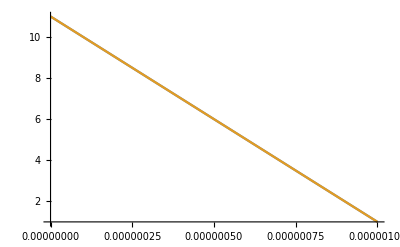

```mathematica
Plot[{Evaluate[x[τ]/.s], (vx0 τ + R + 10R)},{τ,0,Abs[(x0 - R)/vx0]},PlotRange->All]
```

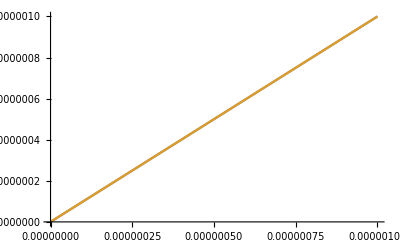

```mathematica
Plot[{Evaluate[t[τ]/.s] , τ},{τ,0,Abs[(x0 - R)/vx0]},PlotRange->All]
```

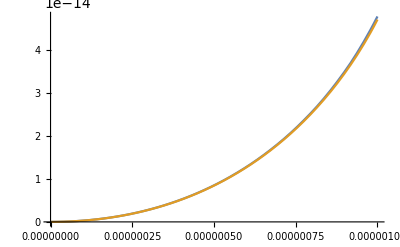

```mathematica
Plot[{Evaluate[z[τ]/.s],TestZ[τ]},{τ,0,Abs[10R/vx0]},PlotRange->All]
```

```mathematica
Clear[G, c, R, v, vx0, ρ, x0]
```

```mathematica
zeqs /. {t'[τ] -> 1}
```

-z''[τ]==(Piecewise[{{(2 G π ρ x[τ])/c^2, R^2-x[τ]^2>0}, {(4 G π R^2 ρ)/(c^2 x[τ]), True}}]) x'[τ] ((2 v)/c-z'[τ])

```mathematica
FullSimplify[DSolve[{-z''[t] == 4 G Pi R^2 ρ vx0/(c^2(vx0 t + x0)) ( 2 v /c - z'[t]), z[0] == 0, z'[0] ==0}, z[t], t]]
```

{{z[t]→(2 v ((c^2 (t vx0+x0) (1-x0^(-(4 G π R^2 ρ)/c^2) (t vx0+x0)^((4 G π R^2 ρ)/c^2)))/vx0+4 G π R^2 t ρ))/(c^3+4 c G π R^2 ρ)}}

```mathematica
ExpandAll[(2 v ((c^2 (t vx0+x0) (1-x0^(-(4 G π R^2 ρ)/c^2) (t vx0+x0)^((4 G π R^2 ρ)/c^2)))/vx0+4 G π R^2 t ρ))/(c^3+4 c G π R^2 ρ)]
```

-7.33333×10^-8+7.33331×10^-8 (11-10000000 t)^(9.31308×10^-7)+0.0666667 t-0.0666665 (11-10000000 t)^(9.31308×10^-7) t

```mathematica
4G Pi ρ/c^2
```

9.31308×10^-7

```mathematica
TestZ[t_]:=(2 v ((c^2 (t vx0+x0) (1-x0^(-(4 G π R^2 ρ)/c^2) (t vx0+x0)^((4 G π R^2 ρ)/c^2)))/vx0+4 G π R^2 t ρ))/(c^3+4 c G π R^2 ρ)
```

```mathematica
G = 6.67*10^(-11);
c = 3*10^8;
R = 1;
v = 1*10^7;
vx0 = -1*10^7;
ρ = 10^20;
x0 = 11 R;
```

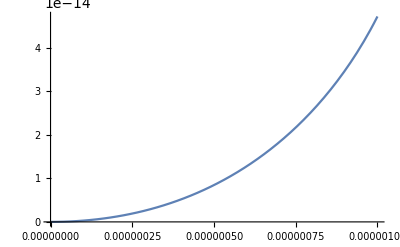

```mathematica
Plot[TestZ[t], {t, 0, Abs[(x0 - R)/vx0]}]
```

```mathematica
P = {{1, 0, 0, 0}, {0, Cos[θ], - Sin[θ], 0}, {0, Sin[θ], Cos[θ], 0}, {0, 0, 0, 1}}
```

{{1,0,0,0},{0,Cos[θ],-Sin[θ],0},{0,Sin[θ],Cos[θ],0},{0,0,0,1}}

```mathematica
Transpose[P]//MatrixForm
```

(1 | 0 | 0 | 0
0 | Cos[θ] | Sin[θ] | 0
0 | -Sin[θ] | Cos[θ] | 0
0 | 0 | 0 | 1)

```mathematica
M = {{1, 0, Ω R /c, 0}, {0, 0, 0, 0}, {Ω R /c, 0, 0, 0}, {0, 0, 0, 0}}
```

{{1,0,(R Ω)/c,0},{0,0,0,0},{(R Ω)/c,0,0,0},{0,0,0,0}}

```mathematica
FullSimplify[P. M.Transpose[P]] // MatrixForm
```

(1 | -(R Ω Sin[θ])/c | (R Ω Cos[θ])/c | 0
-(R Ω Sin[θ])/c | 0 | 0 | 0
(R Ω Cos[θ])/c | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Integrate[Sin[θ] Sin[θ], {θ, 0, 2 Pi}]
```

π